```mathematica
(* Numerically solve mu if beta is within delta_ distance of 1*)
Clear[muSolve];
muSolve[beta_?NumericQ,N_?NumericQ,lambdaI_?NumericQ,kapI_?NumericQ,meank_?NumericQ,delta_:5]:=
Module[{mu,eqn,sol,betaEff},
(*---case 1: |beta-1| <delta->implicit equation---*)
If[Abs[beta-1]<delta,
betaEff=Max[1,beta];(*your max(1,beta) rule*)
eqn=kapI==N*Hypergeometric2F1[1,1/beta,1+1/beta,-(N/2)^beta/((mu*lambdaI*kapI)^betaEff)];
sol=Quiet@FindRoot[eqn,{mu,1/10},(*reasonable initial guess*)WorkingPrecision->40,AccuracyGoal->15,PrecisionGoal->15];
Return[Re[mu]/. sol];];
(*---case 2:beta>1->analytic formula---*)
If[beta>1,Return[(beta*Sin[Pi/beta])/(2 Pi meank)];];
(*---case 3:beta<1->analytic formula---*)
If[beta<1,Return[(1-beta)/(2^beta)*(N^(beta-1))/meank];];
(*fallback (should never be reached)*)Return[$Failed]]
```

```mathematica
ClearAll[βs, βIs, βJs, Ns, μIs, μJs]
```

```mathematica
βIs=Table[i,{i,1/5,2,1/10}];
βJs=Table[i,{i,1/5,2,1/10}];
Ns = Table[10^i,{i,2,8,1}];
μIs=Table[muSolve[βi,n,3,10,10],{n,Ns},{βi,βIs}];
μJs=Table[muSolve[βj,n,4,10,10],{n,Ns},{βj,βJs}];
μIs//Dimensions
```

{7,19}

```mathematica
Clear[inner];
inner[Δ_?NumericQ,κI_,κJ_,λI_,λJ_,n_,βI_, βJ_,μI_,μJ_]:=NIntegrate[n/(2π)*(1/(1+(Max[0,Re[(n/(2π)θ)/(μI*κI*λI)^Max[1,1/βI]]])^βI)(1/(1+(Max[0,Re[(n/(2π)Abs[θ-Δ])/(μJ*κJ*λJ)^Max[1,1/βJ]]])^βJ)+1/(1+(Max[0,Re[(n/(2π)(π-Abs[π-θ-Δ]))/(μJ*κJ*λJ)^Max[1,1/βJ]]])^βJ))),{θ,0,π},Method->{"LocalAdaptive","SymbolicProcessing"->0}]
```

```mathematica
progress=0; (*Initialize progress counter*)
total=Length[βIs]*Length[Ns]; (*Total number of iterations*)
resultnew=Parallelize[Table[
progress++; (*increment progress*)
Monitor[{Ns[[j]],Exp[-3]*1/π NIntegrate[(Exp[inner[Δ,10,10,3,4,Ns[[j]],βIs[[i]], βJs[[i]],μIs[[j,i]],μJs[[j,i]]]]-1-inner[Δ,10,10,3,4,Ns[[j]],βIs[[i]],βJs[[i]], μIs[[j,i]],μJs[[j,i]]]),{Δ,0,π},Method->{"LocalAdaptive","SymbolicProcessing"->0}]},Column[{ProgressIndicator[progress/total],Row[{"Currently evaluating: Ns = ",Ns[[j]],", β = ",βIs[[i]]}]}]],
{i,1,Length[βIs]},{j,1,Length[Ns]}]];
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$34$574419`Δ near {Notebook$$34$574419`Δ} = {3.30163×10^-21}. NIntegrate obtained 1.04337×10^-17 and 4.48205×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$34$574419`Δ near {Notebook$$34$574419`Δ} = {1.32962×10^-21}. NIntegrate obtained 6.68072×10^-17 and 6.98402×10^-18 for the integral and error estimates.

```mathematica
resultnew // Dimensions
```

{19,7,2}

```mathematica
poverlap = Parallelize[Table[{Ns[[j]],1-(1-resultnew[[i,j,2]])^N[Ns[[j]]/2.5]},{i,1,Length[βIs]},{j,1,Length[Ns]}]];
```

```mathematica
poverlap//Dimensions
```

{19,7,2}

```mathematica
fits=Table[{βIs[[#]],a/.NonlinearModelFit[Table[{Log[poverlap[[#,i,1]]],Log[poverlap[[#,i,2]]]},{i,j-2,j}],a*x+b,{a,b},x]["BestFitParameters"]}&/@Range[Length[βIs]],{j,{4, 5, 6, 7}}]
```

{{{1/5,-0.99627},{3/10,-0.99623},{2/5,-0.995961},{1/2,-0.994225},{3/5,-0.983679},{7/10,-0.931226},{4/5,-0.777854},{9/10,-0.560654},{1,-0.366526},{11/10,-0.221033},{6/5,-0.120271},{13/10,-0.0562245},{7/5,-0.0209719},{3/2,-0.00567399},{8/5,-0.00100875},{17/10,-0.000109532},{9/5,-7.02462×10^-6},{19/10,-2.66226×10^-7},{2,-6.02017×10^-9}},{{1/5,-0.999668},{3/10,-0.999645},{2/5,-0.999582},{1/2,-0.999249},{3/5,-0.995266},{7/10,-0.954174},{4/5,-0.766564},{9/10,-0.497817},{1,-0.289681},{11/10,-0.154428},{6/5,-0.0733815},{13/10,-0.0295183},{7/5,-0.0093265},{3/2,-0.00209786},{8/5,-0.000303107},{17/10,-0.0000261005},{9/5,-1.31903×10^-6},{19/10,-4.02344×10^-8},{2,-8.00487×10^-10}},{{1/5,-1.0006},{3/10,-1.00109},{2/5,-1.00159},{1/2,-1.00181},{3/5,-0.998724},{7/10,-0.969213},{4/5,-0.755386},{9/10,-0.448937},{1,-0.234907},{11/10,-0.109557},{6/5,-0.0442337},{13/10,-0.0146378},{7/5,-0.00374593},{3/2,-0.000755729},{8/5,-0.0000900165},{17/10,-6.30911×10^-6},{9/5,-2.61514×10^-7},{19/10,-6.22091×10^-9},{2,-8.28413×10^-11}},{{1/5,-1.00032},{3/10,-1.00203},{2/5,-1.00478},{1/2,-1.00877},{3/5,-1.00694},{7/10,-0.977669},{4/5,-0.766289},{9/10,-0.376511},{1,-0.186584},{11/10,-0.0711094},{6/5,-0.0230831},{13/10,-0.00591051},{7/5,-0.00220632},{3/2,-0.000498715},{8/5,-6.0504×10^-6},{17/10,1.86603×10^-6},{9/5,1.57393×10^-7},{19/10,3.78169×10^-9},{2,-2.50939×10^-11}}}

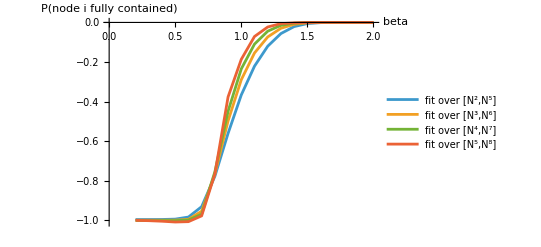

```mathematica
ListLinePlot[fits,AxesLabel->{"beta","P(node i fully contained)"},PlotLegends->{"fit over [N^2,N^5]","fit over [N^3,N^6]","fit over [N^4,N^7]","fit over [N^5,N^8]"}]
```